```mathematica
t1=Table[Import["/home/noel/Documents/Caltech/Courses/CDS 232/Project/Code/t1.csv","Data"]];
t2=Table[Import["/home/noel/Documents/Caltech/Courses/CDS 232/Project/Code/t2.csv","Data"]];
t3=Table[Import["/home/noel/Documents/Caltech/Courses/CDS 232/Project/Code/t3.csv","Data"]];
```

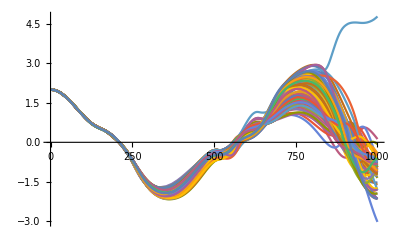

```mathematica
ListLinePlot[Table[t1[[All,t]],{t,1,121}]]
ListLinePlot[Table[t2[[All,t]],{t,1,121}]]
ListLinePlot[Table[t3[[All,t]],{t,1,121}]]
```

```mathematica
ListPointPlot3D[Table[Transpose[{t1[[All,t]],t2[[All,t]],t3[[All,t]]}],{t,1,20}]]/.Point[a___]:>{Thick,Line[a]}
```

```mathematica
max = 1000;
c1 = Flatten[Table[{t,t1[[t,i]]},{i,1,2},{t,max}],1];
Animate[ListLinePlot[c1[[1;;n]],PlotRange->{{0,max},{-6,6}}],{n,1,max,1},AnimationRunning->False]
```